# Three-loop on-shell propagator

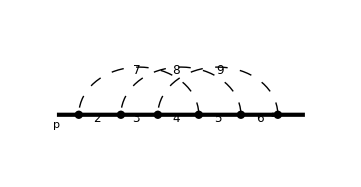
-Graphics-
(*The first entry in the basis, see below, is the irreducible numerator*)

## Finding reduction rules

#### Initialization

```mathematica
<<LiteRed`;
SetDirectory[NotebookDirectory[]];
SetDim[d];
Declare[{l,r,k,p},Vector];
sp[p,p]=1;
```

#### Defining the basis and searching for the symmetries

```mathematica
NewBasis[p3,{l-k,sp[p-l]-1,sp[p-l-r]-1,sp[p-l-r-k]-1,sp[p-r-k]-1,sp[p-k]-1,l,r,k},{l,r,k},Directory->"p3 dir"];(*Basis definition. sp[p,r] is the irreducible numerator.*)
GenerateIBP[p3]
(*IBP generation. Can be also invoked by passing GenerateIBP->True option in NewBasis call*)
AnalyzeSectors[p3,{0,__}](*Zero and simple sectors determination. The second argument is a pattern which claims that the sectors with sp[p,r] in the denominator should not be analyzed*)
FindSymmetries[p3](*Finding unique and mapped sectors.*)
```

#### Searching for the reduction rules and saving

```mathematica
Timing[SolvejSector/@UniqueSectors[p3]]
```

```mathematica
DiskSave[p3](*Saving.*)
Quit[](*Quitting the kernel*)
```

## Manual modifications

#### Initialization

```mathematica
Quit
```

```mathematica
<<LiteRed`;(*Loading the package*)
SetDirectory[NotebookDirectory[]];
(*Setting working directory*)
SetDim[d];(*d stands for the dimensionality*)
Declare[{l,r,k,p},Vector];(*vector variables*)
sp[p,p]=1;(*on-shellness condition*)
```

```mathematica
<<"p3 dir/p3";(*Loading the basis*)
```

#### Graphs

```mathematica
AttachGraph[js[p3,0,1,1,1,1,1,1,1,1],{
{1->2,"1"},
{2->3,"1"},
{3->4,"1"},
{4->5,"1"},
{5->6,"1"},
{1->4,"0"},
{2->5,"0"},
{3->6,"0"},
{0->1,"p"},
{6->0,"p"}
}];(*Attach the graph to the highest sector possible. The graphs for the subsectors are determined automatically. The external legs should start/end at vertex number 0. The internal vertices should be positive integer. The order of the internal lines should correspond to the order of denominators in the sector.*)
SetOptions[GraphPlot,MultiedgeStyle->0.3,VertexRenderingFunction->({If[#2>0,Black,Blue],Disk[#1,0.03]}&),EdgeRenderingFunction->(Replace[#3,{
"1"->{Thick,Black,Line[#1]},
"0"->{Thin,Black,Dashed,Line[#1]},
"p"->{Thickness[0.01],Blue,Line[#1]},
_->Line[#1]
}]&)];
(*Embellish the graph output by standard Mathematica means*)
```

```mathematica
GraphPlot/@jGraph/@MIs[p3](*Draw all masters*)
```

#### Manual modification of the reduction rules

The integral j[p3,0,0,1,0,1,1,1,0,0] with the numerator sp[l,p] added is known to be expressible in terms of the integrals  j[p3,0,0,0,1,0,1,1,1,0] and j[p3,0,0,0,1,1,1,0,0,0], see,e.g., JHEP 1102 (2011) 102 [1010.1334].
So, we can manually take this into account and addd the rule for the elimination of the integral j[p3,0,0,2,0,1,1,1,0,0]:

```mathematica
jnum=Toj[p3,j[p3,0,0,1,0,1,1,1,0,0]sp[l,p]](*The integral with the numerator*)
```

```mathematica
{{extrarule}}=Solve[IBPReduce[jnum]==+(2d-5)/(2d-4)j[p3,0,0,0,1,0,1,1,1,0]+1/4 j[p3,0,0,0,1,1,1,0,0,0],j[p3,0,0,2,0,1,1,1,0,0]];
extrarule
```

```mathematica
p3/:jRules[p3,0,0,1,0,1,1,1,0,0]=Append[jRules[p3,0,0,1,0,1,1,1,0,0],extrarule];(*Add this rule to the rules for {p3,0,1,0,1,1,1,0,0,0} sector*)
MIs[p3]^=DeleteCases[MIs[p3],j[p3,0,0,2,0,1,1,1,0,0]];(*Also remove j[p3,0,1,0,1,2,1,0,0,0] from the masters list*)
```

```mathematica
DiskSave[p3];(*Save to disk*)
Quit[]
```

## Reduction

#### Reduction

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Setting working directory*)
<<LiteRed`;(*Loading the package*)
SetDim[d];(*d stands for the dimensionality*)
Declare[{l,r,k,p},Vector];(*vector variables*)
sp[p,p]=1;(*on-shellness condition*)
```

```mathematica
<<"p3 dir/p3";
```

```mathematica
Timing[IBPReduce[j[p3,-1,1,1,1,1,1,1,1,1],DWeight->2]](*The reduction of some j[…]. The above example takes 1-2 min.*)
```

```mathematica
Timing[IBPReduce[LoweringDRR[p3,0,1,1,1,1,1,1,1,1],"lDRR[011111111]"]]
(*takes about 20min*)
```

```mathematica
Timing[IBPReduce[RaisingDRR[p3,0,1,1,1,1,1,1,1,1],"rDRR[011111111]"]]
(*takes about 20min*)
```